# Basics From Calculus

## Derivatives and Finite Differences

For f:ℝ→ℝ and x∈ℝ
	f'[x]=lim_(h->0) (f[x+h]-f[x])/h

For f:ℝ^n→ℝ and and x,u∈ℝ^n
	∂_u f | = | lim_(h->0) (f[x+ h u ]-f[x])/h
(∂f)/(∂x_i) | = | lim_(h->0) (f[x+ h e_i ]-f[x])/h
Df | = | {∂_1 f,∂_2 f,…,∂_n f}
where ∂_i f=∂f/∂x_i and we have skipped writing down the x dependence.

A derivative of a derivative is a second derivative.  The Hessian of  f:ℝ^n→ℝ 
is the n×n symmetric matrix of second derivatives
	(∂f)/(∂x_i∂x_j) | = | ∂_i (∂_j f) | = | ∂_j (∂_i f)
DDf_(i,j) | = | H_(i,j) | = | ∂_ij f  
Calculus courses usually cover finite Difference(FD) approximations

  | Forward Diff | Centered Diff
f'[x] | (f[x+h]-f[x])/h | (f[x+h]-f[x-h])/(2h)
f''[x] | (f[x+2h]-2f[x+h]+f[x])/h^2  | (f[x+h]-2f[x]+f[x-h])/h^2
∂_i f[x] | (f[x+he_i]-f[x])/h | (f[x+he_i]-f[x-he_i])/(2h)
∂_(i,j) f[x] | (f[x+he_i+ he_j]-f[x+he_i]- f[x+he_j]+ f[x])/h^2 | (f[x+he_i+ he_j]-f[x+he_i-he_j]- f[x+he_j-he_i]+ f[x-he_i-he_j])/h^2

Taylor Series (TS) show that centered differences are more accurate with error behavior described by the TS error terms.

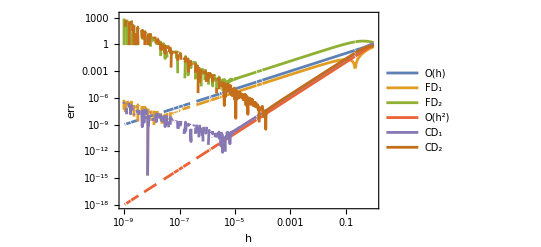

```mathematica
f[x_]:= Cos[x + Exp[ Sin[Log[1+x^2]]]]
x=1.5;
SetOptions[LogLogPlot,GridLines->Automatic,MaxRecursion->4,Frame->True];
LogLogPlot[{
h,Abs[f'[x]-(f[x+h]-f[x])/h],Abs[f''[x]-(f[x+2h]-2f[x+h]+f[x])/h^2],
h^2,Abs[f'[x]-(f[x+h]-f[x-h])/(2h)],Abs[f''[x]-(f[x+h]-2f[x]+f[x-h])/h^2]
},{h,10^-9, 1},
FrameLabel->{"h","err"},
PlotLegends->{"O(h)","FD_1","FD_2","O(h^2)","CD_1","CD_2"}]
```

## Taylor Series

For f:ℝ→ℝ
	f[x_0+h]=f[x_0]+h f'[x_0]+1/2 h^2 f''[x_0]+O(h^3)
For f:ℝ^n→ℝ and u∈ℝ^n
	f[x_0+h u]=f[x_0]+h g_0.u+1/2 h^2 u.H_0.u+O(h^3)
where g_0=Df[x_0] and H_0=DDf[x_0].

A critical point of f:ℝ^n→ℝ satisfies g=Df[x_*]=0_n. 
 A critical point of f is a local minimum if H=DDf[x_*] is positive definite.   
 A critical point of f is a saddle if H=DDf[x_*] is indefinite.

```mathematica
n=2;
{λ1,λ2}={1.2,-1.3};
Q=Orthogonalize[RandomReal[{-1,1},{n,n}]];
H=Q.DiagonalMatrix[{λ1,λ2}].Qᵀ;
TabView[{
"H"->MatrixForm[H],
"3D"->Plot3D[ 1/2{x1,x2}.H.{x1,x2},{x1,-1,1},{x2,-1,1}],
"Cont"->ContourPlot[ 1/2{x1,x2}.H.{x1,x2},{x1,-1,1},{x2,-1,1}]
},2]
```

123

```mathematica
n=3;
{λ1,λ2,λ3}={1.2,-1.3,-0.5};
Q=Orthogonalize[RandomReal[{-1,1},{n,n}]];
H=Q.DiagonalMatrix[{λ1,λ2,λ3}].Qᵀ;
TabView[{
"H"->MatrixForm[H],
"Cont"->ContourPlot3D[ 1/2{x1,x2,x3}.H.{x1,x2,x3},{x1,-1,1},{x2,-1,1},{x3,-1,1},Contours->10,PlotLegends->Automatic,
PlotLabel->Eigenvalues[H]]
},2]
```

12

## Constrained and Unconstrained Optimization

Our target is to minimize an objective function f[x] subject to some equality constraints c_i[x]=0 for i∈ℰ and some inequality constraints c_i[x]≥0 for i∈ℐ.  The c stands for constraint. The script ℰ stands for Equality. The script ℐ stands for inequality.

We are going to assume throughout that the objective function f and all the constraint functions c are differentiable. The feasible set
	Ω={x:c_i[x]=0 for i∈ℰ and c_i[x]≥0for i∈ℐ} 
does not need to have a smooth boundary.

We seek 
	f^*=min_(x∈Ω) f[x] 
and more importantly the x^* that gives f^*=f[x^*].  It is common in papers and code to write 
	x^*=argmin_(x∈Ω)f[x].
Simple box constraints 
	l_i≤x_i≤u_i for i=1 to n
are usually specified and treated separately in algorithms and code. The mnemonic is l for lower and u for upper.  If l_1=-∞ and u_1=+∞ then 
 	-∞<=x_1≤∞
 has no effect.

Any number of inequality constraints makes sense. More than n equality constraints does not really make sense.

### Constraint Pics

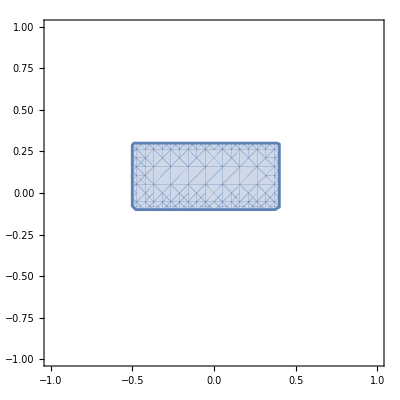

```mathematica
RegionPlot[And[-0.5<x1<0.4,-0.1<x2<0.3],{x1,-1,1},{x2,-1,1}]
```

```mathematica
RegionPlot3D[And[-0.5<x1<0.4,-0.1<x2<0.3, 0.1<x3<0.2],{x1,-1,1},{x2,-1,1},{x3,-1,1},PlotPoints->40]
```

-Graphics3D-

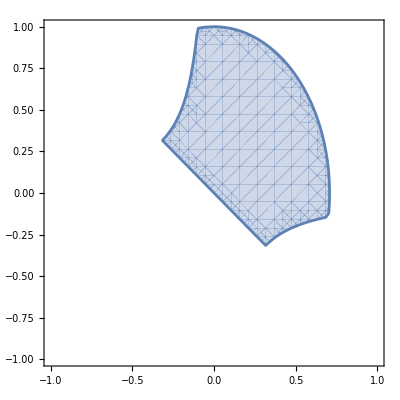

```mathematica
RegionPlot[And[1-( 2 x1^2+x2^2)>0,0.1+x1*x2>0,x1+x2>0],{x1,-1,1},{x2,-1,1}]
```

```mathematica
RegionPlot3D[And[x1+x2+x3>0,
1-( 2 x1^2+x2^2)>0,0.1+x1*x2>0,x1+x2>0],{x1,-1,1},{x2,-1,1},{x3,-2,2},
PlotPoints->40]
```

-Graphics3D-

```mathematica
RegionPlot3D[And[-0.3<x1+x2+x3<0.3,
1-( 2 x1^2+x2^2)>0,0.1+x1*x2>0,x1+x2>0,-0.1+x1+x2+x3>0],{x1,-1,1},{x2,-1,1},{x3,-2,2},
PlotPoints->40]
```

-Graphics3D-

## Definitions for Unconstrained Optimization

For f:ℝ^n→ℝ and no constraints argmin f[x]
	x^* is a global min if f[x^*]≤f[x] for all x
	x^* is a strict global min if f[x^*]<f[x] for all x≠x_*
	x^* is a local min if f[x^*]≤f[x^*+u] for all ||u||≤ϵ
	x^* is a strict local min if f[x^*]≤f[x^*+u] all 0< ||u||≤ϵ

A function f:ℝ^n→ℝ is convex if for 0≤α≤1
	f[α x +(1-α)y]≤α f[x]+(1-a)f[y]. 
It is strictly convex if for 0<α<1 and x≠y
	f[α x +(1-α)y]<α f[x]+(1-a)f[y]

## Definitions for Constrained Optimization

For f:ℝ^n→ℝ and no constraints argmin_(x∈ Ω) f[x] if x^* is feasible i.e. x^*∈Ω then
	x^* is a global min if f[x^*]≤f[x] for all x∈Ω
	x^* is a strict global min if f[x^*]<f[x] for all x∈Ω and x≠x_*
	x^* is a local min if f[x^*]≤f[x^*+u] for all ||u||≤ϵ with x^*+u∈Ω
	x^* is a strict local min if f[x^*]≤f[x^*+u] all 0< ||u||≤ϵ withx^*+u∈Ω

When it comes to writing down equations we will have some technical conditions on the faces, edges, and corners etc of the feasible set Ω.

## Theorems for Unconstrained Optimization (Calculus II and III)

1) If f:ℝ^n→ℝ is smooth a local minimizer of f satisfies Df(x^*)=0 and the Hessian H=DDf[x^*] has no negative eigenvalues. 
2) If f:ℝ^n→ℝ is smooth and Df(x^*)=0 and the Hessian H=DDf[x^*] has all positive eigenvalues then x^* is a strict local minimizer of f.
Critical points satisfy Df(x)=0. Symmetric matrices with all positive eigenvalues are SPD (Symmetric Positive Definite). Symmetric matrices with no negative eigenvalues are Symmetric Semi Positive Definite which is sometimes abbreviated to SSPD.

Unconstrained optimization algorithms try to find critical points with SPD Hessians.   All such points are local minimizer.  Unless there is a tie only one of these points is a global minimizer!  Our algorithms will try to compute local minimizers.

## Theorems for Constrained Optimization (III)

Most Calculus III classes present Lagrange Multipliers for equality constraints.  For two equality constraints c_1[x]=0 and c_2[x]=0 you introduce two Lagrange multipliers λ_1 and λ_2 and form the Lagrangian 
	ℒ[x,λ]=f[x]-λ_1 c_1[x]-λ_2 c_2[x]
The basic theorem in your Calculus course is that a local minimizer satisfies 
	Df[x^*]-λ_1 Dc_1[x^*]-λ_2 Dc_2[x]=0
and the constraints c_1[x^*]=c_2[x^*]=0.

```mathematica
?Cont
```

```mathematica
f[{x1_,x2_,x3_}]:=x1^2+x2^2
c1[{x1_,x2_,x3_}]:=x1+x2-x3^2
c2[{x1_,x2_,x3_}]:= x2*x3+2/10
Show[
ContourPlot3D[f[{x1,x2,x3}],
{x1, -2,2},{x2,-2,2},{x3,-2,2},
ContourStyle->Opacity[0.5],
ColorFunction->"TemperatureMap",
Contours->10],
ContourPlot3D[{c1[{x1,x2,x3}]==0, c2[{x1,x2,x3}]==0},
{x1, -2,2},{x2,-2,2},{x3,-2,2},
ContourStyle->{Orange,Green}]
]
```

```mathematica
?ContourPlot3D
```

```mathematica
ContourPlot3D[{c1[{x1,x2,x3}]==0, c2[{x1,x2,x3}]==0},
{x1, -2,2},{x2,-2,2},{x3,-2,2},
MeshStyle->{Orange, Green},
ColorFunction->Function[{x1,x2,x3},Hue[f[{x1,x2,x3}]]]
]
```

-Graphics3D-

1) If f:ℝ^n→ℝ is smooth a local minimizer of f satisfies Df(x^*)=0 and the Hessian H=DDf[x^*] has no negative eigenvalues. 
2) If f:ℝ^n→ℝ is smooth and Df(x^*)=0 and the Hessian H=DDf[x^*] has all positive eigenvalues then x^* is a strict local minimizer of f.
Critical points satisfy Df(x)=0. Symmetric matrices with all positive eigenvalues are SPD (Symmetric Positive Definite). Symmetric matrices with no negative eigenvalues are Symmetric Semi Positive Definite which is sometimes abbreviated to SSPD.

Unconstrained optimization algorithms try to find critical points with SPD Hessians.   All such points are local minimizer.  Unless there is a tie only one of these points is a global minimizer!  Our algorithms will try to compute local minimizers.

```mathematica
H.x
```

-2.48388

```mathematica
f[{x1_,x2_}]:=
```

### Basic Example

This is much clearer with an example. The function from f:ℝ^3→ℝ^2
	f[x]={x_3+x_1 x_2,x_1 x_2+Cos[x_1+Sin[x_3]]}
is easy to implement.  Here is code to compute it in small steps with the work variables stored in a sequence of “work” variables.

```mathematica
f[{x1_,x2_,x3_}]:= Module[{w1,w2,w3,w4,w5},
w1=x1*x2;
w2=x3+x1*x2;
w3=Sin[x3];
w4=x1+w3;
w5=Cos[w4];
{w2,w5}
]
```

Functions always need to be tested.  This is far from a complete test!

```mathematica
x={0.2,1.4,0.6};
f[x]
```

{0.88,0.72163}

Here is a forward mode Algorithmic Differentiation (AD) code for the function.

```mathematica
df[{x1_,x2_,x3_},{dx1_,dx2_,dx3_}]:= Module[
{w1,w2,w3,w4,w5,dw1,dw2,dw3,dw4,dw5},
dw1=dx1*x2+x1*dx2;
w1=x1*x2;
dw2=dx3+dw1;
w2=x3+w1;
dw3=Cos[x3]*dx3;
w3=Sin[x3];
dw4=dx1+dw3;
w4=x1+w3;
dw5=-Sin[w4]*dw4;
w5=Cos[w4];
{{w2,w5},{dw2,dw5}}
]
```

We need to test this trick.

{{0.88,0.72163},{-2.8,1.80418}}

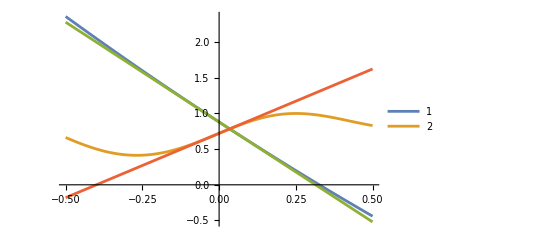

```mathematica
x={0.2,1.4,0.6};
dx={0.2,1.6,-3.4};
h=0.01;
{{f1,f2},{df1,df2}}=df[x,dx]
Plot[{f[x+ h dx]⟦1⟧,f[x+ h dx]⟦2⟧,
f1+h df1,f2+h df2},
{h, -0.5,0.5},
PlotLegends->{"1","2"}]
```

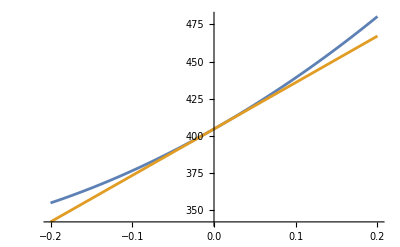

```mathematica
n=12;
{x0,dx0}=RandomReal[{-1,1},{2,n}];
{f0,df0}=dRosen[x0,dx0];
h=0.01;
FD=(Rosen[x0+h dx0]-Rosen[x0])/h;
CD=(Rosen[x0+h dx0]-Rosen[x0-h dx0])/h;
Plot[{Rosen[x0+ϵ dx0],f0+ϵ df0},{ϵ,-0.2,0.2}]
```

You can do the same thing again top get a directional second derivative as well.

```mathematica
ddRosen[x_List,dxa_List,dxb_List]:= Module[{n=Length[x],η=100.0,s=0.0,ds=0.0,dds=0.0},
Do[
dds=ds-2(1-dxb⟦i⟧)dxa⟦i⟧+
2*η*(
(dxb⟦i+1⟧-2x⟦i⟧dxb⟦i⟧)(dxa⟦i+1⟧-2x⟦i⟧dxa⟦i⟧)
+
(x⟦i+1⟧-x⟦i⟧^2)(0.0-2dxb⟦i⟧dxa⟦i⟧)
);
ds=ds-2(1-x⟦i⟧)dxa⟦i⟧+η*(2(x⟦i+1⟧-x⟦i⟧^2)(dxa⟦i+1⟧-2x⟦i⟧dxa⟦i⟧));
s=s+(1-x⟦i⟧)^2+η*(x⟦i+1⟧-x⟦i⟧^2)^2,
{i,1,n-1}];
{s,ds,dds}
]
```

{875.531,421.366,983.065}

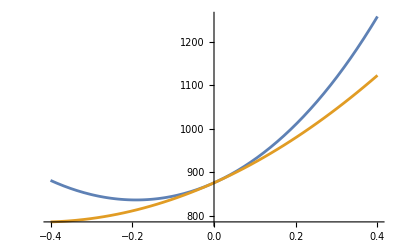

```mathematica
n=12;
{x0,dxa}=RandomReal[{-1,1},{2,n}];
{f0,df0,ddf0}=ddRosen[x0,dxa,dxa]
Plot[{Rosen[x0+ϵ dxa],f0+ϵ df0 +ϵ^2/2 ddf0},{ϵ,-0.4,0.4}]
```

### Rosenbrock Example

This is much clearer with an example. The generalized Rosenbrock function from f:ℝ^n→ℝ
	f(x)=∑_(i=1)^(n-1) (100(x_(i+1)-x_i^2)^2+(1-x_i)^2
is a standard optimization test problem.  Here is code to compute it.

```mathematica
Rosen[x_List]:= Module[{n=Length[x],η=100.0,s=0.0},
Do[
s=s+(1-x⟦i⟧)^2+η*(x⟦i+1⟧-x⟦i⟧^2)^2,
{i,1,n-1}];
s
]
```

Functions always need to be tested.  This is not a complete test!

```mathematica
n=12;
{Rosen[ConstantArray[1,n]],Rosen[RandomReal[{-1,1},n]]}
```

{0.,875.416}

Here is a forward mode Algorithmic Differentiation code for the Rosenbrock function.

```mathematica
dRosen[x_List,dx_List]:= Module[{n=Length[x],η=100.0,s=0.0,ds=0.0},
Do[
ds=ds-2(1-x⟦i⟧)dx⟦i⟧+2*η*((x⟦i+1⟧-x⟦i⟧^2)(dx⟦i+1⟧-2x⟦i⟧dx⟦i⟧));
s=s+(1-x⟦i⟧)^2+η*(x⟦i+1⟧-x⟦i⟧^2)^2,
{i,1,n-1}];
{s,ds}
]
```

We need to test this trick.

```mathematica
n=12;
{x0,dx0}=RandomReal[{-1,1},{2,n}];
{f0,df0}=dRosen[x0,dx0];
h=0.01;
FD=(Rosen[x0+h dx0]-Rosen[x0])/h;
CD=(Rosen[x0+h dx0]-Rosen[x0-h dx0])/h;
Plot[{Rosen[x0+ϵ dx0],f0+ϵ df0},{ϵ,-0.2,0.2}]
```

-Graphics-

You can do the same thing again top get a directional second derivative as well.

```mathematica
ddRosen[x_List,dxa_List,dxb_List]:= Module[{n=Length[x],η=100.0,s=0.0,ds=0.0,dds=0.0},
Do[
dds=ds-2(1-dxb⟦i⟧)dxa⟦i⟧+
2*η*(
(dxb⟦i+1⟧-2x⟦i⟧dxb⟦i⟧)(dxa⟦i+1⟧-2x⟦i⟧dxa⟦i⟧)
+
(x⟦i+1⟧-x⟦i⟧^2)(0.0-2dxb⟦i⟧dxa⟦i⟧)
);
ds=ds-2(1-x⟦i⟧)dxa⟦i⟧+η*(2(x⟦i+1⟧-x⟦i⟧^2)(dxa⟦i+1⟧-2x⟦i⟧dxa⟦i⟧));
s=s+(1-x⟦i⟧)^2+η*(x⟦i+1⟧-x⟦i⟧^2)^2,
{i,1,n-1}];
{s,ds,dds}
]
```

```mathematica
n=12;
{x0,dxa}=RandomReal[{-1,1},{2,n}];
{f0,df0,ddf0}=ddRosen[x0,dxa,dxa]
Plot[{Rosen[x0+ϵ dxa],f0+ϵ df0 +ϵ^2/2 ddf0},{ϵ,-0.4,0.4}]
```

{875.531,421.366,983.065}

-Graphics-

## XX

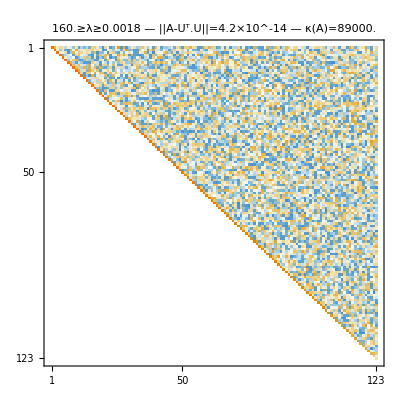

```mathematica
m=123;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
U=CholeskyDecomposition[A];λs=Eigenvalues[A];
{res,λMax,λMin,κ}=Map[SetPrecision[#,2]&,
{Norm[A-Uᵀ.U],Max[λs],Min[λs],Max[λs]/Min[λs]}];
MatrixPlot[U,
PlotLabel->StringForm["``≥λ≥`` — ||A-Uᵀ.U||=`` — κ(A)=``",
λMax,λMin,res,κ]
]
```

Here is an inefficient implementation.

```mathematica
m=1234;A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
U=A;
Do[
Do[
U⟦j,j;;m⟧-=U⟦k,j;;m⟧ U⟦k,j⟧/U⟦k,k⟧,
{j,k+1,m}];
U⟦k,k;;m⟧/=√U⟦k,k⟧,
{k,1,m}];
U=UpperTriangularize[U];
MatrixPlot[U,PlotLabel->Norm[A-Uᵀ.U]]
```

-Graphics-

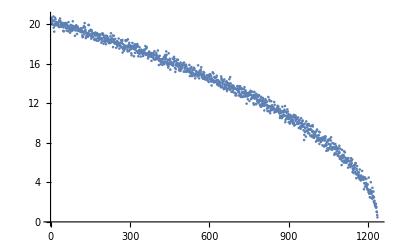

```mathematica
ListPlot[ Diagonal[U]]
```

# Cholesky QR

It would be efficient to get Cholesky to compute a QR decomposition for a Tall Skinny matrix A∈ℝ^(m×n) (a matrix with m>>n ) because if
	A=Q.R
then Aᵀ.A=(Rᵀ.Qᵀ).(Q.R)=Rᵀ.(Qᵀ.Q).R=Rᵀ.R∈ℝ^(n×n) and we can compute
	Q=A.R^-1
We are going to see why this is fast.  We are going to see why this is not used.  We are going to see how people know how to fix this.  We are going to experiment with a potentially better way to fix it.

Cholesky QR is almost always a bit faster!

```mathematica
{m,n}={12000,300};
A=RandomReal[{-1,1},{m,n}];
{{t1,x}=Timing[{Q1,R1}=QRDecomposition[A];Q1=Q1ᵀ;],
{t2,x}=Timing[R2=CholeskyDecomposition[Aᵀ.A];Q2=A.Inverse[R2];],
t1/t2}
Map[Norm[#,"Frobenius"]&,{A-Q1.R1,Q1ᵀ.Q1-IdentityMatrix[n],A-Q2.R2,Q2ᵀ.Q2-IdentityMatrix[n]}]
```

{{0.234375,Null},{0.046875,Null},5.}

{3.16066×10^-13,5.36223×10^-15,1.27929×10^-13,4.71192×10^-15}

Cholesky QR can be tricked into giving inaccurate answers when the built-in Householder QR has no problem.

```mathematica
{m,n}={400,6};
Q=Orthogonalize[RandomReal[{-1,1},{n,m}]]ᵀ;
A=Q.HilbertMatrix[n];
{Q1,R1}=QRDecomposition[A];Q1=Q1ᵀ;
R2=CholeskyDecomposition[Aᵀ.A];Q2=A.Inverse[R2];
Map[Norm[#,"Frobenius"]&,{A-Q1.R1,Q1ᵀ.Q1-IdentityMatrix[n],A-Q2.R2,Q2ᵀ.Q2-IdentityMatrix[n]}]
```

{6.80012×10^-16,9.09364×10^-16,7.01103×10^-16,0.00228002}

The Hilbert matrix is a badly conditioned matrix!

```mathematica
n=8;
BadMat=HilbertMatrix[n];
σs=SingularValueList[1.0*BadMat];
TabView[{
MatrixPlot[BadMat,
PlotLabel->StringForm["κ=``", Max[σs]/Min[σs]]],
MatrixForm[BadMat]
}]
```

12

Some people worked out you can fix the CholeskyQR by doing it twice.

```mathematica
{m,n}={400,6};
Q=Orthogonalize[RandomReal[{-1,1},{n,m}]]ᵀ;
A=Q.HilbertMatrix[n];
{Q1,R1}=QRDecomposition[A];Q1=Q1ᵀ;
R2=CholeskyDecomposition[Aᵀ.A];Q2=A.Inverse[R2];
R3=CholeskyDecomposition[Q2ᵀ.Q2]; R32=R3.R2;
Q3=A.Inverse[R32];
Map[Norm[#,"Frobenius"]&,{
A-Q1.R1,Q1ᵀ.Q1-IdentityMatrix[n],
A-Q2.R2,Q2ᵀ.Q2-IdentityMatrix[n],
A-Q3.R3.R2,Q3ᵀ.Q3-IdentityMatrix[n]}]
```

{7.37581×10^-16,8.14456×10^-16,5.97972×10^-16,0.0023002,7.48159×10^-16,3.34078×10^-9}

Of course if twice is good three times is possibly better.

```mathematica
ImproveQR[A_,{Q_,R_}]:= Module[{RInner,RNew},
RInner=CholeskyDecomposition[Qᵀ.Q];
RNew=RInner.R;
{A.Inverse[RNew], RNew}
]
```

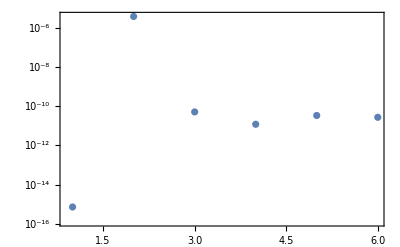

```mathematica
{m,n}={123,5};
Q=Orthogonalize[RandomReal[{-1,1},{n,m}]]ᵀ;
A=Q.HilbertMatrix[n];
Clear[Q];
{Q[0],R[0]}=QRDecomposition[A];Q[0]=Q[0]ᵀ;
R[1]=CholeskyDecomposition[Aᵀ.A];Q[1]=A.Inverse[R[1]];
Do[
{Q[i+1],R[i+1]}=ImproveQR[A,{Q[i],R[i]}],
{i,1,4}]
ListLogPlot[
Table[
Norm[Q[i]ᵀ.Q[i]-IdentityMatrix[n],"Frobenius"],
{i,0, 5}],
Frame->True,
GridLines->Automatic,
PlotRange->All]
```

# Differentiating Cholesky

Here is our inefficient Cholesky implementation.  We can differentiate every single line of arithmetic in the code!

```mathematica
m=12;A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
U=A;
Do[
Do[
U⟦j,j;;m⟧-=U⟦k,j;;m⟧ U⟦k,j⟧/U⟦k,k⟧,
{j,k+1,m}];
U⟦k,k;;m⟧/=√U⟦k,k⟧,
{k,1,m}];
U=UpperTriangularize[U];
MatrixPlot[U,PlotLabel->Norm[A-Uᵀ.U]]
```

This is going to be easier to see if I write a function for the plain vanilla Cholesky

```mathematica
PVCholesky[A_]:= Module[{m=Length[A],U=A},
Do[
Do[
U⟦j,j;;m⟧-=U⟦k,j;;m⟧ U⟦k,j⟧/U⟦k,k⟧,
{j,k+1,m}];
U⟦k,k;;m⟧/=√U⟦k,k⟧,
{k,1,m}];
U=UpperTriangularize[U]
]
```

As soon as you write a function you should test it!

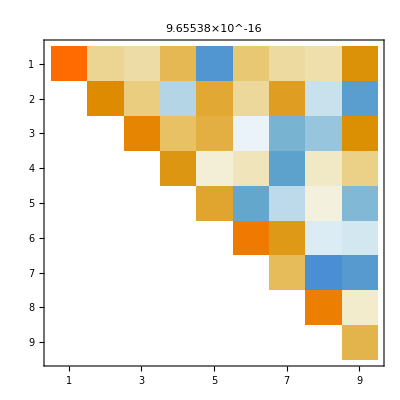

```mathematica
m=9;
A=RandomReal[{-1,1},{m,m}]; A= A.Aᵀ;
U=PVCholesky[A];
MatrixPlot[U,PlotLabel->Norm[A-Uᵀ.U]]
```

I want to modify differentiate this function so that it returns U[ϵ] satisfying Uᵀ.U=A+ϵ Id as well as a matching matrix Ud satisfying the matrix equation
	 Udᵀ.U+Uᵀ.Ud=0+Id
you get when you differentiate with respect to ϵ.  Ud is the derivative of U with respect to the scalar parameter ϵ.  The plan is to approximate U[0] using the Taylor series expansion
	U[0]=U[ϵ]-ϵ Ud[ϵ]+O(ϵ^2)
The error in the approximation
	u[0]≈u[ϵ]-ϵ Ud[ϵ]
is less than some constant C ϵ^2.  The plan is to add a small multiple ϵ of the identity onto A to make the Cholesky computation more accurate for U[ϵ] and Ud[ϵ] then approximate U[0] with u[0]≈u[ϵ]-ϵ Ud[ϵ].

```mathematica
ADCholesky[A_]:= Module[{m=Length[A],U=A,dU},
dU=IdentityMatrix[m];
Do[
Do[
dU⟦j,j;;m⟧-=dU⟦k,j;;m⟧ U⟦k,j⟧/U⟦k,k⟧+U⟦k,j;;m⟧ dU⟦k,j⟧/U⟦k,k⟧ -U⟦k,j;;m⟧ U⟦k,j⟧ dU⟦k,k⟧/U⟦k,k⟧^2;
U⟦j,j;;m⟧-=U⟦k,j;;m⟧ U⟦k,j⟧/U⟦k,k⟧,
{j,k+1,m}];
dU⟦k,k;;m⟧=dU⟦k,k;;m⟧/√U⟦k,k⟧-0.5U⟦k,k;;m⟧dU⟦k,k⟧/U⟦k,k⟧^1.5;
U⟦k,k;;m⟧=U⟦k,k;;m⟧/√U⟦k,k⟧,
{k,1,m}];
U=UpperTriangularize[U];
{U, dU}
]
```

The question is what from to fit to the thing.  We know that in the problem case there is at least one pivot headed towards zero.

```mathematica
{m,r}={54,6};
Q=Orthogonalize[RandomReal[{-1,1},{r,m}]]ᵀ;
A=Q.HilbertMatrix[r];S=Aᵀ.A;
SingularValueList[S]
U=CholeskyDecomposition[S];
ϵ1=10^-12;
QComp=A.Inverse[U];
ϵ1=10^-20;
U1=CholeskyDecomposition[S+ϵ1 IdentityMatrix[r]];
QComp1=A.Inverse[U1];
Map[Norm,{IdentityMatrix[r]-QCompᵀ.QComp,IdentityMatrix[r]-QComp1ᵀ.QComp1}]
```

{2.62084,0.0587388,0.000266392,3.79146×10^-7,1.58024×10^-10}

{0.00176323,0.00176323}

```mathematica
QC
SingularValueList[S]
ϵ0=10.0^-8;
{U,dU}=ADCholesky[S+ϵ0 IdentityMatrix[r]];
Map[Norm,{S+ϵ0 IdentityMatrix[r]-Uᵀ.U,dUᵀ.U+Uᵀ.dU-IdentityMatrix[r]}]
```

{2.97867,0.103448,0.000963415,3.91618×10^-6,7.67041×10^-9,7.14501×10^-12}

{6.99104×10^-16,4.51876×10^-14}

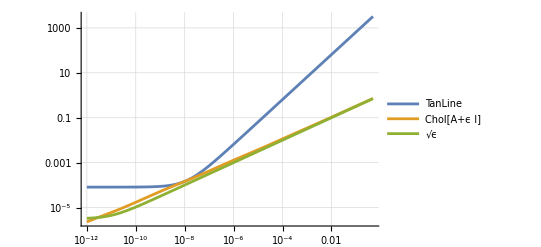

```mathematica
{i,j}={r,r};
LogLogPlot[ {U⟦i,j⟧+(ϵ-ϵ0) dU⟦i,j⟧,CholeskyDecomposition[S+ϵ IdentityMatrix[r]]⟦i,j⟧,(ϵ+10^-11)^(1/2)},{ϵ,10^-12, 0.5},
GridLines->Automatic,
PlotLegends->{"TanLine","Chol[A+ϵ I]","√ϵ"}]
```

```mathematica
Series[ √(x+ϵ),{ϵ,0,3}]
```

√x+ϵ/(2 √x)-ϵ^2/(8 x^(3/2))+ϵ^3/(16 x^(5/2))+O[ϵ]^4

```mathematica
Normal[√x+ϵ/(2 √x)-ϵ^2/(8 x^(3/2))+ϵ^3/(16 x^(5/2))+O[ϵ]^4]
```

√x+ϵ/(2 √x)-ϵ^2/(8 x^(3/2))+ϵ^3/(16 x^(5/2))

```mathematica
Map[Dimensions,{A,U}]
```

{{54,8},{8,8}}

```mathematica
CholeskyDecomposition[S+10^-17 IdentityMatrix[r]]
```

CholeskyDecomposition::posdef: The matrix {{1.53977,0.9,0.654545,0.519697,0.433042,0.372148,0.32679,0.291585,0.263409},{0.9,0.549768,0.409091,«3»,0.212148,0.190183,0.172468},«5»,{«1»},«1»} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition[{{1.53977,0.9,0.654545,0.519697,0.433042,0.372148,0.32679,0.291585,0.263409},{0.9,0.549768,0.409091,0.329545,0.277389,0.240185,0.212148,0.190183,0.172468},{0.654545,0.409091,0.308032,0.25,0.211538,0.183883,0.162912,0.146401,0.13303},{0.519697,0.329545,0.25,0.203866,0.173077,0.150824,0.133883,0.120501,0.109636},{0.433042,0.277389,0.211538,0.173077,0.147283,0.128571,0.114286,0.102976,0.0937763},{0.372148,0.240185,0.183883,0.150824,0.128571,0.112385,0.1,0.0901786,0.0821779},{0.32679,0.212148,0.162912,0.133883,0.114286,0.1,0.0890514,0.0803571,0.0732668},{0.291585,0.190183,0.146401,0.120501,0.102976,0.0901786,0.0803571,0.0725495,0.0661765},{0.263409,0.172468,0.13303,0.109636,0.0937763,0.0821779,0.0732668,0.0661765,0.0603847}}]

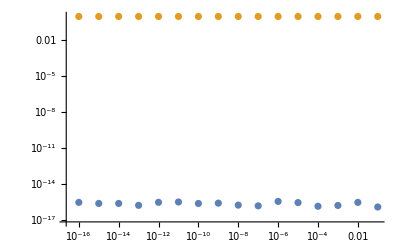

```mathematica
ϵs=10.0^(-Range[1,16]);
Data=Table[
U=CholeskyDecomposition[S+ϵ IdentityMatrix[r]];
QComp=A.Inverse[U];
{ϵ,Norm[S+ϵ IdentityMatrix[r]-Uᵀ.U],Norm[IdentityMatrix[r]-QCompᵀ.QComp]},
{ϵ,ϵs}];
ListLogLogPlot[{Data⟦All,{1,2}⟧,Data⟦All,{1,3}⟧},
PlotRange->All]
```

Approximation form.
The first pivot (diagonal element) that gets small does so something like √(α + ϵ) and the associated off diagonal elements get big something like 1/√(α+ϵ)

# Shifted Cholesky

As a reminder the Cholesky algorithm “chol(A)” needs A to be “sufficiently” positive definite to compute the upper triangular factor L(A) .  Even if it completes L(A) can be relatively inaccurate if the SPD matrix A has big and small eigenvalues which is quantified by te condition number κ(A)=(λ_max(A))/(λ_min(A)).

The easiest way to fix a badly conditioned matrix is to add a multiple of the identity 	
	κ(A+ϵ I)  =(λ_max(A+ϵ I))/(λ_min(A+ϵ I))=(λ_max(A)+ϵ)/(λ_min(A)+ϵ)
The question is how to approximate L(A) from a computation of L(A+ϵ I).

Our first task is to make a badly conditioned square matrix.

```mathematica
Clear[U]
p=6;
λs=100.0^Range[-p,0,1]; Q=Orthogonalize[RandomReal[{-1,1},{p+1,p+1}]];
A=Q.DiagonalMatrix[λs].Qᵀ;
U[ϵ_]:=CholeskyDecomposition[A+ϵ IdentityMatrix[p+1]];
ϵs=5.0^Range[-18,0,1];
Data=Table[ U[ϵ],{ϵ,ϵs}];
i=1;
TabView[Table[
i->ListLogLogPlot[
Table[{ϵs,Abs[Data⟦All,i,j⟧]}ᵀ,{j,i,p+1}],PlotLegends->Table[Subscript[u, i,j],{j,i,p+1}],
PlotRange->All,PlotStyle->Thin,Frame->True,GridLines->Automatic,Joined->True,Mesh->All],
{i,1,p+1}]]
```

1234567

```mathematica
Clear[U]
p=6;
λs=100.0^Range[-p,0,1]; Q=Orthogonalize[RandomReal[{-1,1},{p+1,p+1}]];
A=Q.DiagonalMatrix[Reverse[λs]].Qᵀ;
U[ϵ_]:=CholeskyDecomposition[A+ϵ IdentityMatrix[p+1]];
ϵs=5.0^Range[-18,0,1];
Data=Table[ U[ϵ],{ϵ,ϵs}];
i=1;
TabView[Table[
i->ListLogLogPlot[
Join[{{ϵs,0.001 +10 ϵs^(1/2)}ᵀ},
Table[{ϵs,Abs[Data⟦All,i,j⟧]}ᵀ,{j,i,p+1}]],
PlotLegends->Join[{"0.001 + √ϵ"},Table[Subscript[u, i,j],{j,i,p+1}]],
PlotStyle->Thin,Frame->True,GridLines->Automatic,Joined->True,Mesh->All],
{i,1,p+1}]]
```

1234567

```mathematica
{ϵs,ϵs^2}ᵀ
```

{{2.62144×10^-13,6.87195×10^-26},{1.31072×10^-12,1.71799×10^-24},{6.5536×10^-12,4.29497×10^-23},{3.2768×10^-11,1.07374×10^-21},{1.6384×10^-10,2.68435×10^-20},{8.192×10^-10,6.71089×10^-19},{4.096×10^-9,1.67772×10^-17},{2.048×10^-8,4.1943×10^-16},{1.024×10^-7,1.04858×10^-14},{5.12×10^-7,2.62144×10^-13},{2.56×10^-6,6.5536×10^-12},{0.0000128,1.6384×10^-10},{0.000064,4.096×10^-9},{0.00032,1.024×10^-7},{0.0016,2.56×10^-6},{0.008,0.000064},{0.04,0.0016},{0.2,0.04},{1.,1.}}

```mathematica
λs
```

{1.×10^-12,1.×10^-10,1.×10^-8,1.×10^-6,0.0001,0.01,1.}